# Mathematica Notebook for PSet-01

Important note: Use Evaluation → Quit Kernel if you run into strange behavior.  Each command you run changes the environment and quitting the kernel will reset the environment / variables.

## Flows on the line.

### Section 2.2: Fixed points and stability

#### Finding the location of fixed points.

The "Solve" command finds solutions to an equation.  Mathematica attempts to use analytical methods to solve the equation exactly (rather than finding a numerical approximation to the solution).

You can use Solve to find the x values associated with fixed points.

Code in Mathematica comes in "cells".  The gray brackets on the right side show you the cells.

To run a Mathematica cell: click in the cell.  Then press shift+return to execute the commands in the cell.

There are a number of details in the function definition command.  Notice the _ after the x, the : before the = and the use of [ ] rather than ( ) or { }.  Once the function is defined, you can call it with an input.

The ; at the end of the line suppresses output.  When it is missing, you'll see the output from running the command.

```mathematica
f[x_] := 4 x^2 - 16;
h[x_] := k1 x^2 - 16;
f[3]
fp = Solve[f[x] == 0, x]
fph = Solve[h[x] == 0, x]
```

20

{{x→-2},{x→2}}

{{x→-4/(√k1)},{x→4/(√k1)}}

For the outputs above, which line of code produced each one?
Functions also often work even if you don't tell Mathematica what the input variable is:

```mathematica
g := 4x^2 - 16
fp = Solve[g== 0, x]
```

{{x→-2},{x→2}}

#### Graphing functions

We can make graphs in Mathematica.

Notice AxesLabel allows you to label your axes and PlotLabel allows you to add a title.  LabelStyle is being used to increase the font sizes.

To plot more than one function on the same axes, put the functions in a list.  Lists start with { and end with } (curly braces).

-Graphics-

-Graphics-

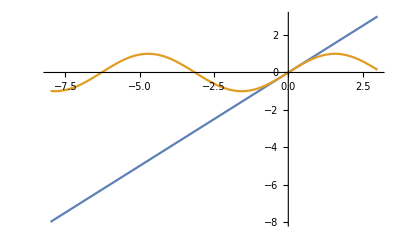

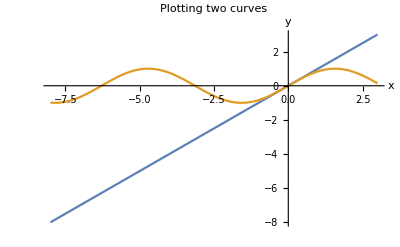

```mathematica
Plot[f[x], {x, -3, 3}]
Plot[g, {x, -3, 3}]
Plot[{x, Sin[x]}, {x, -8, 3}]
Plot[{x, Sin[x]}, {x, -8, 3},AxesLabel->{x, y},PlotLabel->"Plotting two curves",LabelStyle->{FontSize,14}]
```

### Section 2.4: Linear stability

Mathematica can find derivatives.  Again, these usually aren't numerical approximations.  Mathematica uses a symbolic toolbox to find the derivative function (when possible).

I give a few different notations for taking a derivative.  derivC will generalize to higher dimensions.  derivB only works when the input to the function is explicitly defined (so for f[x] but not for g).

/. allows you to temporarily replace a variable or parameter with a value (the value applies just for that one line of the code).  
/.fp replaces x with each value of the fixed points returned by the Solve command up above.

Notice that {x} is a list of variables (it's a list with only one entry in it).

```mathematica
deriv = D[g, x]
derivB = f'[x] 
derivC = Grad[g,{x}]
deriv /. fp
```

8 x

8 x

{8 x}

{-16,16}

### Section 2.8: Numerical approximations of solution curves

In addition to a symbolic toolbox, Mathematica can also do numerical calculations.  We can use Mathematica to generate numerical approximations of the solutions curves of a differential equation.

NDSolve takes in a differential equation and an initial condition.  It returns an approximated solution curve.

f[x] is defined near the top of this file.  You'll need to run the cell where f[x] is defined before the commands below will work.

Notice that we used the f[x] form of the function to set up the differential equation in NDSolve.

We need to explicitly specify that solutions are functions of the form x[t] when we write the differential equation.  (Notice x'[t] and f[x[t]]).

To plot the solution curves, we use /.soln to replace x[t] with the specific x[t] solution curve generated by the NDSolve command.

{{x→InterpolatingFunction[…]}}

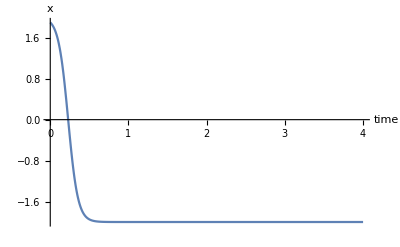

```mathematica
timemax = 4;
soln = NDSolve[{x'[t] == f[x[t]], x[0] == 1.9}, x, {t, 0, timemax}]
Plot[x[t] /. soln, {t, 0, timemax}, PlotRange -> All, AxesLabel->{time,x}]
```

It's possible to turn the initial condition into a parameter by using ParametricNDSolve.  If you do that, then the initial condition isn't specified during the NDSolve call.

I plot a number of different approximate solution curves by making a table of initial conditions, substituting each entry in the table as the initial condition for the numerical solution, and asking Mathematica to Evaluate my expression in order to produce a list of solution curves.

The Table has x0 initial conditions that go from -4 to 2 in steps of 0.75.

The solutions from ParametricNDSolve are functions of time indexed by the parameter x0.  To access the single approximate solution for x0 = 1 we would write x[1][t]/.soln

Try including a value of x0 of 2.1 in the plot.  This is a solution that diverges towards ∞.  
(I typed ∞ by typing 'esc inf esc' where esc is the escape key).

{x→ParametricFunction[<>]}

InterpolatingFunction[…][t]

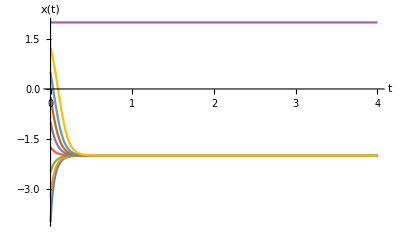

```mathematica
tmax = 4;
f[x_] := 4 x^2 - 16;
soln = ParametricNDSolve[{x'[t] == f[x[t]], x[0] == x0}, x, {t, 0, tmax}, {x0}]
x[1][t]/.soln
Plot[
 Evaluate[Table[x[x0][t] /. soln, {x0, -4, 2, 0.75}]], {t, 0, tmax}, 
 PlotRange -> All,AxesLabel->{t,"x(t)"}]
```

Alternatively, we can specify a list of initial conditions to use (rather than generating an evenly spaced set).

{x→ParametricFunction[<>]}

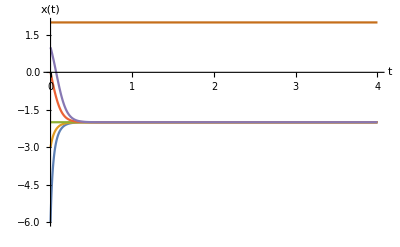

```mathematica
tmax = 4;
f[x_] := 4 x^2 - 16;
soln = ParametricNDSolve[{x'[t] == f[x[t]], x[0] == x0}, x, {t, 0, tmax}, {x0}]
IClist={-6, -3, -2, 0, 1, 2};
Plot[
 Evaluate[Table[x[IClist[[index]]][t] /. soln, {index, 1, Length[IClist],1}]], {t, 0, tmax}, 
 PlotRange -> All,AxesLabel->{t,"x(t)"}]
```

### Extra: Solving a differential equation symbolically

Sometimes a nonlinear differential equation has a simple enough form that it is possible to generate a solution to the initial value problem (where the differential equation and an initial solution value have been specified) using analytic methods.

Other times, finding a solution isn't tractable.

{{x→Function[{t},(78.-2. ⅇ^(16. t))/(39.+1. ⅇ^(16. t))]}}

{{x→Function[{t},(2+10 ⅇ^(16 t))/(1-5 ⅇ^(16 t))]}}

-Graphics-

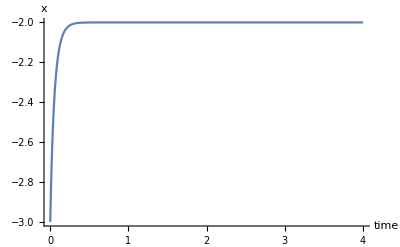

Set::shape: Lists {DSolve`DSolveSpecialFirstOrderODEDump`c$58106,DSolve`DSolveSpecialFirstOrderODEDump`e$58106} and {-x} are not the same shape.

DSolve::bvnul: For some branches of the general solution, the given boundary conditions lead to an empty solution.

{}

```mathematica
timemax = 4;
f[x_] := 4 x^2 - 16;
exactsoln = DSolve[{x'[t] == f[x[t]], x[0] == 1.9}, x, {t, 0, timemax}]
exactsoln2 = DSolve[{x'[t] == f[x[t]],x[0]==-3}, x, {t, 0, timemax}]
Plot[x[t] /. exactsoln, {t, 0, timemax}, PlotRange -> All, AxesLabel->{time,x}]
Plot[x[t] /. exactsoln2, {t, 0, timemax}, PlotRange -> All, AxesLabel->{time,x}]
exactsolnfailure = DSolve[{x'[t] == x[t]-Cos[x[t]], x[0] == 0.3}, x, {t, 0, timemax}]
```

```mathematica
xp = c1-8t;
eqn = 2/((Exp[xp]-Exp[-xp])/(Exp[xp]+Exp[-xp]))
```

(2 (ⅇ^(c1-8 t)+ⅇ^(-c1+8 t)))/(ⅇ^(c1-8 t)-ⅇ^(-c1+8 t))

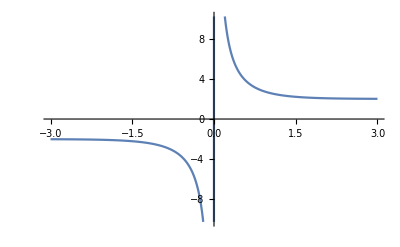

2.

```mathematica
Plot[eqn/.t->0,{c1,-3,3}]
eqn/.t->0./.c1->10
```

```mathematica
(2-2 ⅇ^(4 (4 t+C[1])))/(1+ⅇ^(4 (4 t+C[1])))/.t->0
```

(2-2 ⅇ^(4 C[1]))/(1+ⅇ^(4 C[1]))

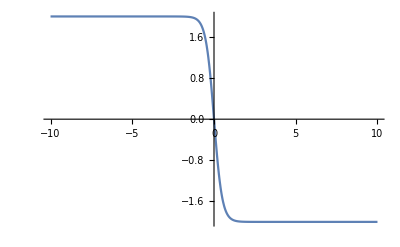

```mathematica
Plot[(2-2Exp[4 c1])/(1+Exp[4 c1]),{c1,-10,10}]
```